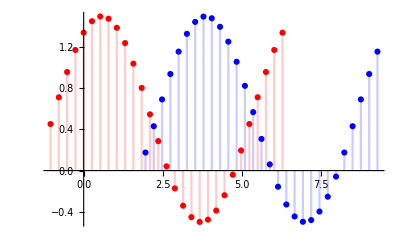

```mathematica
(*时移*)
Show[DiscretePlot[Sin[x+1]+0.5,{x,-π/3,2π,π/12},PlotStyle->Red],
	DiscretePlot[Sin[x+4]+0.5,{x,-π/3+3,3+2π,π/12},PlotStyle->Blue],
	PlotRange->All]
```

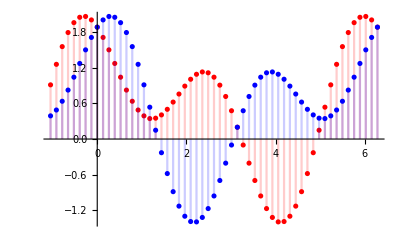

```mathematica
(*时间反转*)
Show[DiscretePlot[Sin[x+1]+Cos[2x+1]+0.5,{x,-π/3,2π,π/24},PlotStyle->Red],
	DiscretePlot[Sin[-x+1]+Cos[-2x+1]+0.5,{x,-π/3,2π,π/24},PlotStyle->Blue],
	PlotRange->All]
```

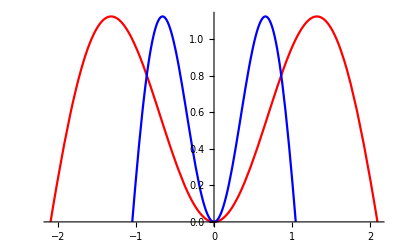

```mathematica
(*时间反转*)
Show[Plot[Sin[x+π/2]+Cos[2(x+π/2)],{x,(-2π)/3,2/3 π},PlotStyle->Red],
	Plot[Sin[2(x+π/4)]+Cos[4(x+π/4)],{x,-π/3,π/3},PlotStyle->Blue],
	PlotRange->All]
```

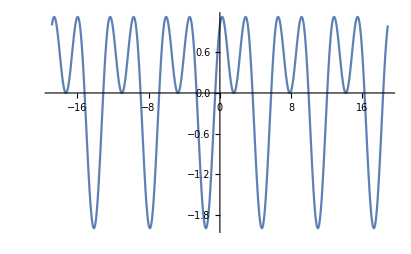

```mathematica
(*周期信号*)
Plot[Sin[x]+Cos[2x],{x,-6π,6π}]
```

```mathematica
(*奇偶信号*)
ClearAll;
(*f[x_]:=Piecewise[{{Sin[x],x≤ 0},{Cos[x],x>0}},x];*)
f[x_]:=Sin[x]+Cos[2x];
Plot[{f[x],1/2(f[x]+f[-x]),1/2(f[x]-f[-x])},{x,-3,3},PlotStyle->{Purple,Blue,Red},PlotLabels->{原函数,偶部,奇部}]
```

-Graphics-

```mathematica
Plot[ⅇ^(ⅉ t),{t,-6π,6π}]
```

-Graphics-

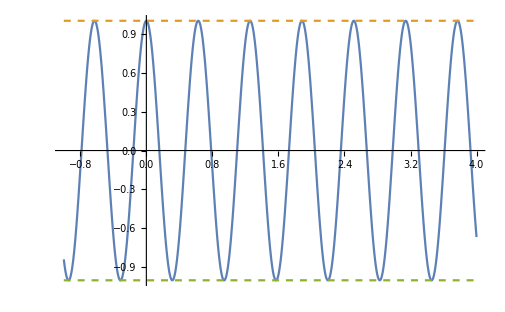

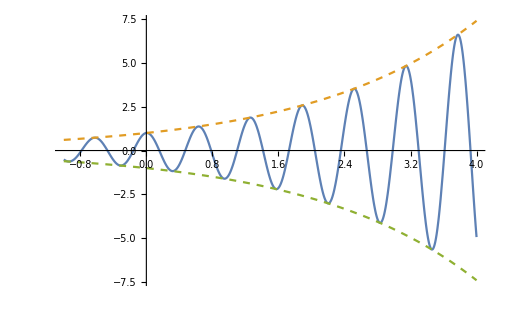

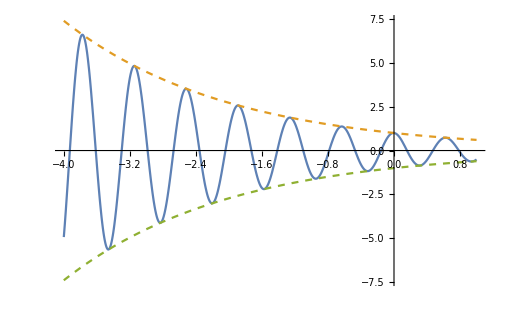

```mathematica
ClearAll;
f[t_,w_,c_,r_]:=Abs[c] ⅇ^(r t)Cos[w t+θ];
g[t_,w_,c_,r_]:=c ⅇ^(r t);
Plot[{f[t,10,1,0],g[t,10,1,0],g[t,10,-1,0]},{t,-1,4},PlotRange->All,PlotStyle->{,Dashed,Dashed}]
Plot[{f[t,10,1,0.5],g[t,10,1,0.5],g[t,10,-1,0.5]},{t,-1,4},PlotRange->All,PlotStyle->{,Dashed,Dashed}]
Plot[{f[t,10,1,-0.5],g[t,10,1,-0.5],g[t,10,-1,-0.5]},{t,-4,1},PlotRange->All,PlotStyle->{,Dashed,Dashed}]
```

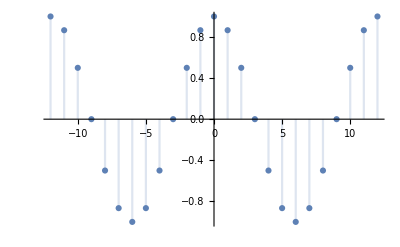

```mathematica
ClearAll;
DiscretePlot[Cos[(2π n)/12],{n,-12,12}]
```